# Sound Shell Model

This notebook is a short tutorial for the SSModel package, which computes gravitational wave spectra from acoustic oscillations following cosmological first-order phase transitions, based on the sound-shell model (JCAP12(2019)062).

It includes SSModel_2f.wl, an extension to the 2-fluid scenario, where sound waves from a phase transition in a dark sector “leak” into the visible sector.

Package structure

\SSModel

BubbleFluidProfiles.wl

SSModel.wl

SSModel_2f.wl

\data

kinetic.wl

gw.wl

gw.2f.wl

Master functions

Profile
Compute the fluid profiles for the phase transition bubbles. This includes the profiles of

velocity

enthalpy

energy density perturbations

GetKineticSpecrum
Get the kinetic spectrum ζ_kin(K) (Eqs. 33 and 41 of 2308.12943). 
If not in kinetic.wl, compute and store the relative spectrum.

OmegaGW
The gravitational wave spectrum Ω_GW(K) (Eq. 51 of 2308.12943)

OmegaGW2f
The 2-fluid gravitational wave spectrum (Eq. 45 of arXiv xx.yy).
Two additional parameters govern this spectrum:

γ≡Γ_int/(H_*) the interaction rate between the two fluids, normalized to the Hubble parameter at the transition time.

r_w≡((w̄)_v)/((w̄)_d) the enthalpy ratio between the visible and dark fluids.

References

Characterization of the GW spectrum from Soundwaves, Roper Pol, Procacci & Caprini (PhysRevD .109.063531)

Leaking Sound Waves: GWs From Dark Sectors Weakly Coupled to the
SM, Finetti, Krichevskii & Kolesova (arXiv:2610.40781).

```mathematica
Quit
```

## Tutorial

## Initialize

```mathematica
SetDirectory[NotebookDirectory[]];
Import["SSModel/SSModel.wl"];
```

Loaded/home/marco/PhD/DarkTransitions/SSModel/BubbleFluidProfiles.wl

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

Auxiliary parameters set to:

c_s^2 →  1/3

Γ_ad →  1.33333

cs2::careful: Redefining cs2 doesn't modify the value of cs. Both are used in the implementation.

```mathematica
Import["SSModel/SSModel_2f.wl"];
```

### Numerics

Define some numerical values

```mathematica
num=<|vw->.9,α->.1,
δτH->1.,HR->.01,
r->10.,γ->10.,
k->1.,q->.1,𝓆->.2,z->.3|>;
ρFrac=1/(1+r)/.num;
```

### Files

```mathematica
FilterDataset[data_Dataset,assoc_Association]:=data[Select[Lookup[#,Keys[assoc]]==Values[assoc]&]](*data[Select[MatchQ@KeyValuePattern[Normal[assoc]]]]*)
FilterDataset[file_String,assoc_Association]:=Module[{data,matching},
data=Get[file];
If[MatchQ[data,_Dataset],
matching=FilterDataset[data,assoc];
Return[matching],
Print[StringTemplate["File `` does not match a dataset"]]
]
]
```

```mathematica
SortDataset[data_Dataset]:=data[SortBy[{"vw","α","SourceDuration","HR","rw","γ"}]]
SortDataset[file_String]:=SortDataset[Get[file]]
SortDataset[file_String,"Overwrite"]:=Module[{d=SortDataset[file]},
Put[d,file];d]
```

```mathematica
KData=Get[$KineticFile];
```

```mathematica
file1f="data/GWSpectra.1f.wl";
GWData=Get[file1f];
```

```mathematica
file2f="data/GWSpectra.2f.wl";
GWData2f=Get[file2f];
```

### Plots

```mathematica
Options[PlotGWAll]={"Data1f"->file1f,"Data2f"->file2f,"PlotSuppression"->True};
PlotGWAll[assoc_,opts:OptionsPattern[{PlotGWAll,Plot}]]:=Module[{one,two,s,supp,data1f,data2f,in},
	data1f=Get[OptionValue["Data1f"]];
	data2f=Get[OptionValue["Data2f"]];
	one=FilterDataset[data1f,assoc][-1,"KOmega"]//Normal;
	two=FilterDataset[data2f,assoc][All,"KOmega"]//Normal;
	supp=If[OptionValue["PlotSuppression"],
	s=Υ2fOver1f["SourceDuration",{10.,10.}]/.assoc;
	 MapAt[s #&,one,{All,2}],
	{}
	];
	PlotGWData[Join[{one,supp},two],
		opts//Evaluate,
		Joined->True,
		ImageSize->Medium,
		PlotStyle->Insert[Table[Automatic,3],Directive[Gray,Thickness[.003]],2],
		PlotLabel->StringTemplate["\!\(\*SubscriptBox[\(ξ\), \(w\)]\)=`vw`   δτH=`SourceDuration`   HR=`HR`"][assoc],
	PlotLegends->{"γ→0","(Υ (γ))/(Υ (γ → 0))","γ→10","γ→100"}
	]
		]
PlotGWAllGammas[vw_,δτH_,HR_,opts:OptionsPattern[]]:=PlotGWAll[
	<|"vw"->vw,"SourceDuration"->δτH,"HR"->HR|>,opts//Evaluate
	]
PlotGWAllGammas[δτH_?NumericQ,opts:OptionsPattern[]]:=Table[PlotGWAllGammas[vw,δτH,HR,opts//Evaluate,ImageSize->Large],
{vw,1.Range[1,9,2]/10},
{HR,{.01,.001}}
]//Flatten//Partition[#,2]&//PlotGrid
PlotGWAllGammas2[vw_?NumericQ]:=Table[PlotGWAllGammas[vw,δτH,HR,ImageSize->Large],
{δτH,{.1,1.}},
{HR,{.01,.001}}
]//Flatten//Partition[#,2]&//Grid
```

```mathematica
cosmoImport[dt_,HR_]:=Import[StringTemplate["cosmoGW/data/KOmega_vw_0.9_dtau_``_HR_``.csv"][dt,HR]][[2;;,{1,6}]]
cosmoImport[dt_,HR_,γ_,r_]:=Import[StringTemplate["cosmoGW/data/KOmega_vw_0.9_dtau_``_HR_``_gamma_``_r_``.csv"][dt,HR,γ,r]][[2;;,{1,6}]]
ClearAll[PlotGWSuppressions]
Options[PlotGWSuppressions]={"Data1f"->file1f,"Data2f"->file2f,"PlotSuppression"->True,"N"->30,"FontSize"->10,"r"->10.};
PlotGWSuppressions[vw_?NumericQ,α_?NumericQ,δτH_?NumericQ,HR_?NumericQ,opts:OptionsPattern[{PlotGWSuppressions,Plot}]]:=Module[{assoc=<|"vw"->vw,"α"->α,"SourceDuration"->δτH,"HR"->HR|>,
	one,two,s,supp,γs,nγ,lowK,highK,lowK2f,highK2f,data2f,in,r=OptionValue["r"],ρFrac,
	fs=OptionValue["FontSize"],
	f1=OptionValue["Data1f"],f2=OptionValue["Data2f"],
	KSpectrum=GetKineticSpectrum[vw,α,cs,"Verbose"->False],
	optsPlot=FilterOptions[Join[{opts},Options[PlotGWSuppressions]],Options[Plot]]
	},
	ρFrac=(1/(1+r));
	one=If[f1=="cosmo",MapAt[ρFrac^2#&,cosmoImport[δτH,HR],{All,2}],
	FilterDataset[Get[f1],assoc][-1,"KOmega"]//Normal
	];
	two=If[f2=="cosmo",γs=If[HR==0.01,{10.},{10.,100.}];
	Table[MapAt[ρFrac^2#&,cosmoImport[δτH,HR,γ,r],{All,2}],{γ,γs}],
	data2f=FilterDataset[Get[f2],assoc];
	γs=Union[data2f[All,"γ"]//Normal];
	data2f[All,"KOmega"]//Normal
	];
	nγ=Length[γs];
	(* Υ2f/Υ1f *)
	Table[s[γ]=Υ2fOver1f[δτH,{γ,r}],{γ,γs}];
	supp=Table[MapAt[s[γ] #&,one,{All,2}],{γ,γs}];
	(* low K *)
	lowK=Table[{K,OmegaGWLowK[K,δτH,KSpectrum,"DensityFraction"->ρFrac]},
	{K,{10.^-3,10.^-2(*2. 10^-2*)}}
	];
	lowK2f=Table[{K,OmegaGW2fLowK[K,δτH,KSpectrum,{γ,r},"DensityFraction"->ρFrac]},
	{γ,γs},
	{K,{10.^-3,10.^-2}}
	];
	(* high K *)
	highK=ComputeOmegaGW[OmegaGWHighK[#,{cs,δτH,HR},KSpectrum,
	"DensityFraction"->ρFrac,
	"Verbose"->False
	]/.assoc&,
	"KRange"->{10.^-3,3 10.^2},
	"N"->OptionValue["N"],
	"DynamicPlot"->False
	][[All,;;2]];
	highK2f=Table[MapAt[s[γ]#&,highK,{All,2}],{γ,γs}];
	PlotGWData[Join[{one},two,(*supp,*){lowK,highK},lowK2f,highK2f],
		optsPlot//Evaluate,
		ImageSize->Medium,
	PlotRange->{{3 10^-4,3 10^2},{10^-20,5 10^-10}},
		PlotStyle->Join[
	Table[Automatic,1+nγ],
	(*Table[Directive[Gray,Thickness[.003]],nγ],*)
	Table[Directive[c[[1]],c[[2]],Thickness[.003]],{c,{{DarkRed,DotDashed},{DarkBlue,Dashed}}}],
	Table[Directive[DotDashed,DarkRed,Thickness[.003]],nγ],
	Table[Directive[Dashed,DarkBlue,Thickness[.003]],nγ]
	],
		PlotLabel->(*"v_w=0.9   τ_swH_*=1   H_*R_*=10^-3"*)(*StringTemplate["v_w=`vw`   τ_swH_*=`SourceDuration`   H_*R_*=`HR`"][<|"vw"->vw,
	"SourceDuration":>(δτH/.(1.->1)),
	"HR":>SuperscriptBox["10",ToString[Round[Log10[HR]]]]|>]*)Row@{"v_w=",vw,"   τ_swH_*=",δτH/.(1.->1),"   H_*R_*=",Superscript[10,Round[Log10[HR]]]},
	PlotLegends->If[(*HR==0.001∧*)δτH==.1,
	Placed[Flatten@{
		Style["Γ_int/H_*=0",fs],
		Table[Style[StringTemplate["Γ_int/H_*=``"][Round@γ],fs],{γ,γs}]
		(*Table[StringTemplate["supp (γ→``)"][γ],{γ,γs}],*)
		(*"low K",
		"high K"*)(*,
	Table[StringTemplate["low K (γ→``)"][γ],{γ,γs}],
		Table[StringTemplate["high K (γ→``)"][γ],{γ,γs}]*)
		},{Top,Right}],
	None]
		]]
PlotGWSuppressions[vw_?NumericQ,opts:OptionsPattern[]]:=Table[PlotGWSuppressions[vw,num[α],δτH,HR,opts//Evaluate],
{δτH,{.01,.1,1.}},
{HR,{.01,.001}}
]//Flatten//Partition[#,2]&
(*PlotGWSuppressions[δτH_?NumericQ,opts:OptionsPattern[]]:=Table[PlotGWSuppressions[vw,num[α],δτH,HR,opts//Evaluate],
{vw,1.Range[1,9,2]/10},
{HR,{.01,.001}}
]//Flatten//Partition[#,2]&*)
AutoComplete[PlotGWSuppressions];
```

## Fluid profiles

```mathematica
(* 2fix: make public when importing from SSModel.wl *)
Import["SSModel/BubbleFluidProfiles.wl"]
```

```mathematica
prof=Profile[ξw=.1,α=.1,"Verbose"->True]//EchoTiming;
AutoComplete[prof];
{vip,wip,λip,shellDom}=Lookup[prof,{"v","w","λ","ShellDomain"}];
{ξm,ξM}=shellDom (* extract domain *);
```

Bubble type →  Def

Running shooting algorithm for target α=0.1

α+ | Bubble`Private`α$193855
ξ_w | 0.1
(ṽ)_+ | 0.0695091
v_+ | 0.0307043
w_- | 0.704881
ξ_sh | 0.57735
w_sh | 1.

α+ | Bubble`Private`α$193889
ξ_w | 0.1
(ṽ)_+ | 0.0700859
v_+ | 0.0301252
w_- | 0.710554
ξ_sh | 0.57735
w_sh | 1.

0.078191

### Inspect profile

```mathematica
Select[prof,NumericQ]//Dataset
```

```mathematica
prof
```

<|v→InterpolatingFunction[…],w→InterpolatingFunction[…],λ→InterpolatingFunction[…],ξw→0.1,vp→0.0301252,vm→0.,wp→1.01904,wm→0.710554,wsh→1.,α+→0.0981313,ShellDomain→{0.1,0.57735},αComputed→0.0999671,αComputedList→{0.101938,0.0999671},α+List→{0.098099,0.0981313},Type→Def|>

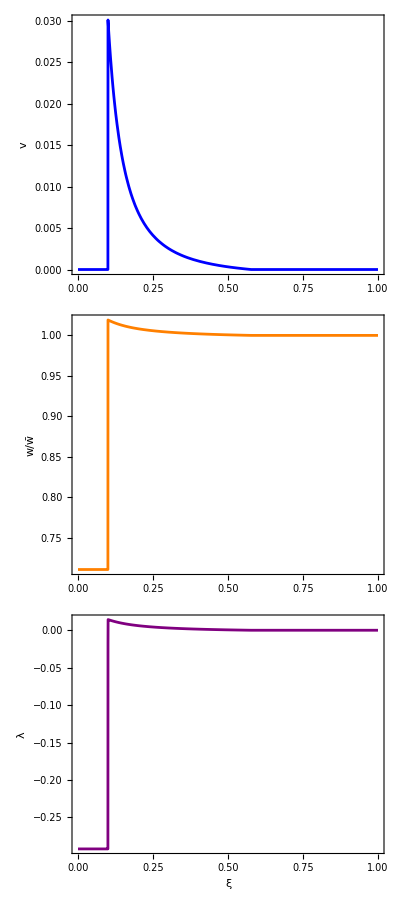

```mathematica
PlotProfile[prof]
```

```mathematica
ManipulateVelocityProfile[]
```

## Kinetic Spectrum (ζ_kin)

Get kinetic spectrum (if not in file, compute it)

```mathematica
KSpectrum=GetKineticSpectrum[.1,.1,cs=1./√3]//Quiet;
AutoComplete[KSpectrum];
Select[KSpectrum,NumericQ]
```

<|vw→0.1,α→0.1,cs→0.57735,Rβ→0.292918,EkOverRstar→80.203,KSpectrumIntegral→0.0000950109,KEnergyDensityFraction→0.00762015|>

### Plot kinetic spectra

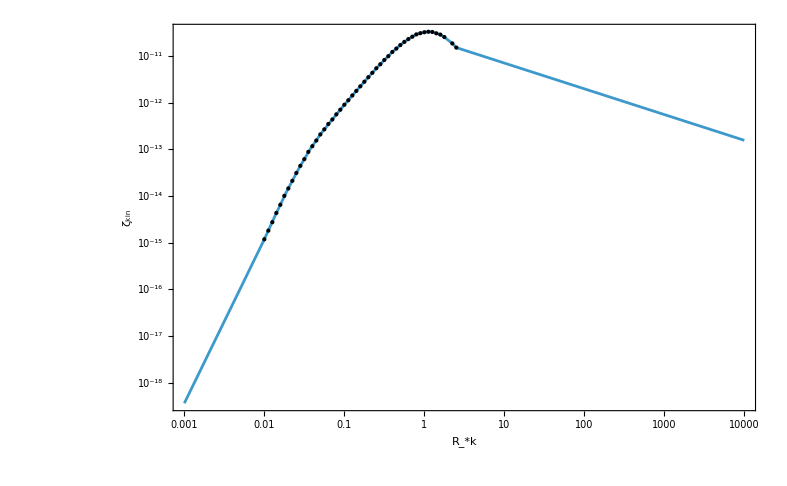

```mathematica
PlotKineticSpectrum[KSpectrum]
```

```mathematica
kinData=Get[$KineticFile];
```

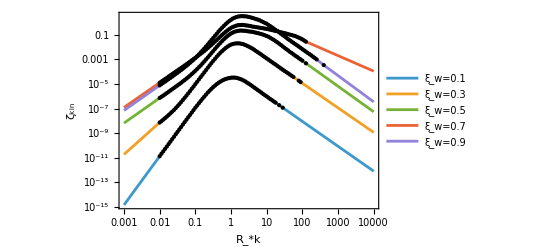

```mathematica
PlotKineticSpectrum[kinData[;;;;2]]
```

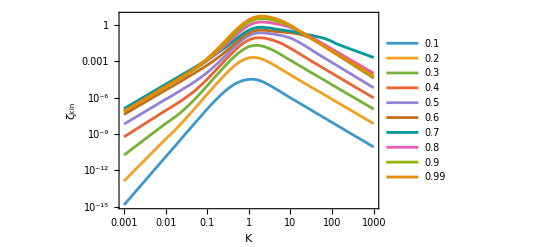

```mathematica
LogLogPlot[Through[Normal[KData[All,"KSpectrum"]][K]]//Evaluate,{K,10^-3,10.^3},FrameLabel->{"K", "ζ_kin"},$PlotOptions//Evaluate,PlotLegends->Normal[KData[All,"vw"]]]
```

### Sound waves amplitudes

```mathematica
{fInt,lInt}=Lookup[KSpectrum,{"f","l"}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
With[{z=10.},
{fInt[10.3]//EchoTiming,lInt[10.3]//EchoTiming}
]
```

0.00011

0.000057

{-0.00696385,-0.0134359}

```mathematica
A2Int[z_]=(*.5 fInt'[z]^2*)1/4(fInt'[z]^2+cs2 lInt[z]^2)
```

1/4 (1/3 (InterpolatingFunction[…][z])^2+(InterpolatingFunction[…][z])^2)

```mathematica
zDomain={10^-2,10^3};
Plot[{
fInt'[z]^2/4,
cs2 lInt[z]^2/4,
A2Int[z],
If[z<1,z^2]fInt'[zDomain[[1]]]^2/zDomain[[1]]^2
},{z,Sequence@@zDomain},ScalingFunctions->{"Log","Log"},
Frame->True,
GridLines->Automatic,
PlotLegends->"Expressions",
PlotStyle->{Red,Darker@Green,Directive[Blue,Opacity[.5]],Directive[Black,Dashed]},
ImageSize->Large,
AxesLabel->{"z","A^2"}
]//EchoTiming
```

0.488936

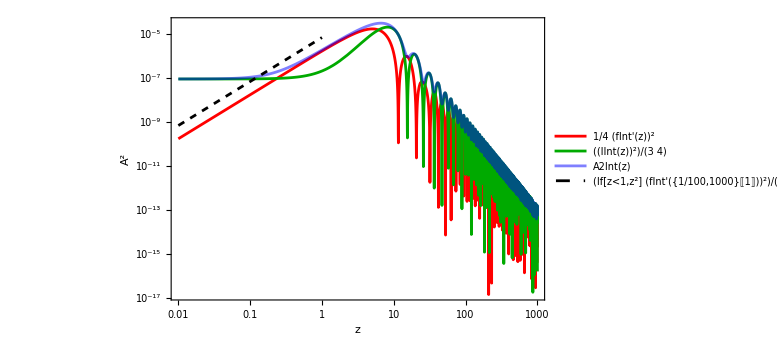

#### Numerical Fits

2do: must extract shock position and fluid velocity from profiles, to determine z_(1,2)

```mathematica
BPL[z_,{fp0_,z1_,a1_}]:=fp0^2 z^2(1+(z/z1)^a1)^(-6/a1)
DBPL[z_,{fp0_,z1_,z2_,a1_,a2_,γ_}]:=fp0^2 z^2(1+(z/z1)^a1)^((γ-2)/a1)(1+(z/z2)^a2)^(-(γ+4)/a2)
```

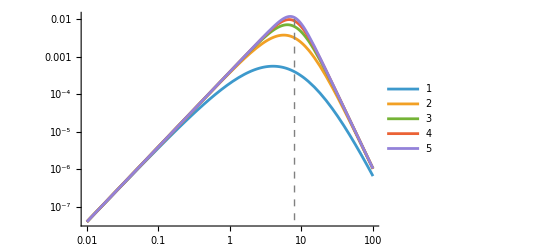

```mathematica
Module[{a1s=Range[1,5],z1=8.},
LogLogPlot[Table[BPL[z,{.02,z1,a1}],{a1,a1s}]//Evaluate,{z,10^-2,10^2},PlotLegends->a1s,Epilog->{Dashed,Gray,InfiniteLine[{Log@z1,0},{0,1}]},GridLines->Automatic]]
```

Select some fit parameter

```mathematica
fp0=-(4π)/3 NIntegrate[ξ^3 vip[ξ],{ξ,ξm,ξM}] (* fInt'[zm]/zm *)
l0=4π NIntegrate[λip[ξ] ξ^2,{ξ,ξm,ξM}]
```

-0.0601878

0.0975371

```mathematica
fp2Fit[z_]:=BPL[z,{fp0,8.,4.}]//Evaluate
```

```mathematica
A2Fit[z_]:=.5fp2Fit[z]
```

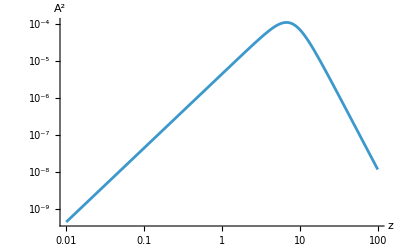

```mathematica
LogLogPlot[A2Fit[z],{z,10^-2,10^2},GridLines->Automatic,AxesLabel->{"z","A^2"}]
```

Fit the actual data

```mathematica
findPeaks[data_List]:=Select[Partition[data,3,1],(#[[1,2]]<#[[2,2]]>#[[3,2]])&][[All,2]];
selectFp2Data[fp2Data_]:=Module[{fp2DataPeaks},
fp2DataPeaks=findPeaks[fp2Data];
Select[fp2Data,#[[1]]<fp2DataPeaks[[1,1]]&]~Join~fp2DataPeaks
]
```

```mathematica
fp2Data=Table[{z,fInt'[z]^2},{z,zs}];
fp2DataEnv=selectFp2Data[fp2Data];
```

```mathematica
fp2EnvBPL=NonlinearModelFit[fp2DataEnv,{BPL[z,{fp0,z1,a1}],z1>0,a1>0},{z1,a1},z]
```

FittedModel[…]

```mathematica
fp2EnvDBPL=NonlinearModelFit[fp2DataEnv,{DBPL[z,{fp0,z1,z2,a1,a2,γ}],0<z1<z2,a1>0,a2>0},{z1,z2,a1,a2,γ},z,Weights->(Sqrt[#2]&),ConfidenceLevel->0.99]
```

FittedModel[…]

```mathematica
Options@NonlinearModelFit
```

{AccuracyGoal→Automatic,ConfidenceLevel→19/20,EvaluationMonitor→None,Gradient→Automatic,MaxIterations→Automatic,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,Tolerance→Automatic,VarianceEstimatorFunction→Automatic,Weights→Automatic,WorkingPrecision→Automatic}

```mathematica
Show[LogLogPlot[fInt'[z]^2,{z,zm,zM},PlotStyle->Gray,PlotLegends->{"Interpolation"},GridLines->Automatic],
ListLogLogPlot[fp2DataEnv,PlotLegends->{"Peaks (+ low tail)"}],
LogLogPlot[{fp2EnvBPL[z],fp2EnvDBPL[z]},{z,zm,zM},PlotStyle->{Red,Directive[Blue,Dashed]},PlotLegends->{"BPL Fit","DBPL Fit"}],
Graphics[{Gray,Dashed,HalfLine[Log@{z1,fp2EnvBPL[z1]}/.fp2EnvBPL["BestFitParameters"],{0,-1}]}]
]
```

-Graphics-

```mathematica
A2Env[z_]:=.5 fp2EnvDBPL[z]
```

### Kinetic energy density

Ω_K=∫_0^∞ dk E_k(τ,τ,k)=∫_0^∞ dk E_k(k)	(eq. 42)
𝒦=∫_0^∞ dK ζ_k(K)  ⇒  Ω_K≈E_k^*/(R_*)𝒦		(eq. 43)

```mathematica
{ζk,EkOverRstar,{Km,KM}}=Lookup[KSpectrum,{"KSpectrum","EkOverRstar","KDomain"}];
```

```mathematica
𝒦=NIntegrate[ζk[K],{K,Km,KM},AccuracyGoal->∞,PrecisionGoal->3,MaxRecursion->∞]
ΩK=EkOverRstar 𝒦
```

0.0794783

0.00874403

```mathematica
(* time-scale for the development of non-linearities in the plasma *)
τstar=1.;
δτnl=SubStar[R]/(√ΩK);
τnl=τstar+δτnl
δτnl/SubStar[R]
```

1.23981

9.09661

### Generate multiple spectra

To generate the spectra of $KineticFile, run the following (~10’)

```mathematica
Table[GetKineticSpectrum[vw,.1,cs,File->"kineticSpectra.wl"]//Quiet,{vw,Join[Range[9]/10.,{.99}]}]
```

## Time integrals (Δ)

```mathematica
Δmn[10.,1.,1.]//EchoTiming
ΔDef[10.,1.,{1.,.1,10.,cs}]//EchoTiming
```

0.003497

0.163476

3.60763

0.0285667

### p_mn plots

#### ΔCi, ΔSi

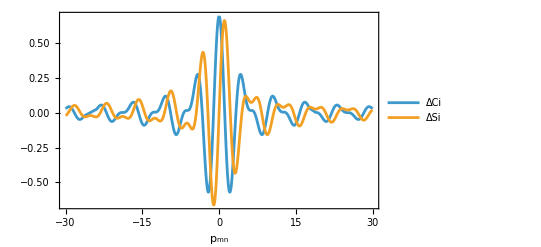

```mathematica
Plot[{ΔCi[δτH,Qmn],ΔSi[δτH,Qmn]}/.num//Evaluate,{Qmn,-30,30},
PlotRange->All,Frame->True,FrameLabel->{"p_mn"},PlotLegends->{"ΔCi","ΔSi"}]
```

#### p_mn

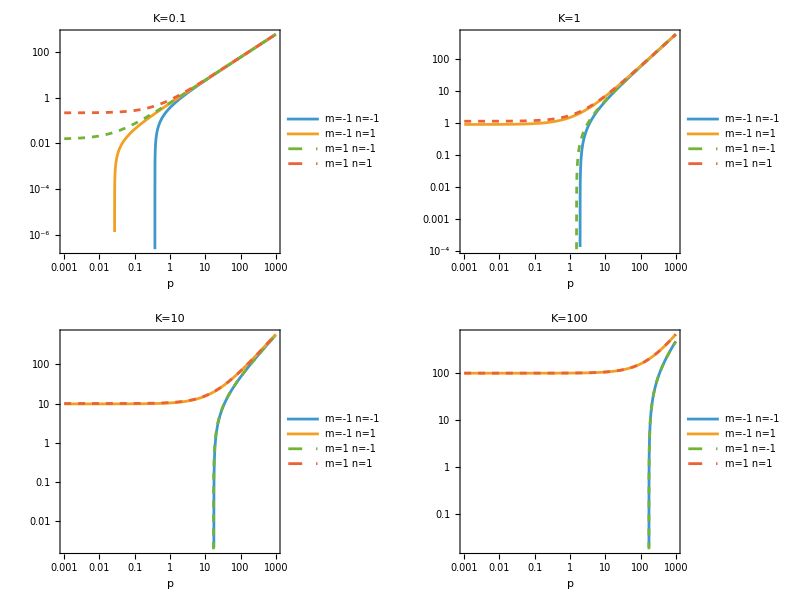

```mathematica
Table[LogLogPlot[Table[pmn[{m,n},{K,Q,𝓆,cs}]/.num,{m,{-1,1}},{n,{-1,1}}]//Evaluate,{Q,10^-3,10^3},
PlotRange->All,Frame->True,FrameLabel->{"p"},
ImageSize->Medium,
PlotStyle->{Dashing[None],Dashing[None],Dashed,Dashed},
PlotLabel->StringTemplate["K=``"][K],
PlotLegends->Placed[Flatten[Table[StringTemplate["m=`` n=``"][m,n],{m,{-1,1}},{n,{-1,1}}],1],{Left,Bottom}]],
{K,10^Range[-1,2]}]//Partition[#,2]&//Grid
```

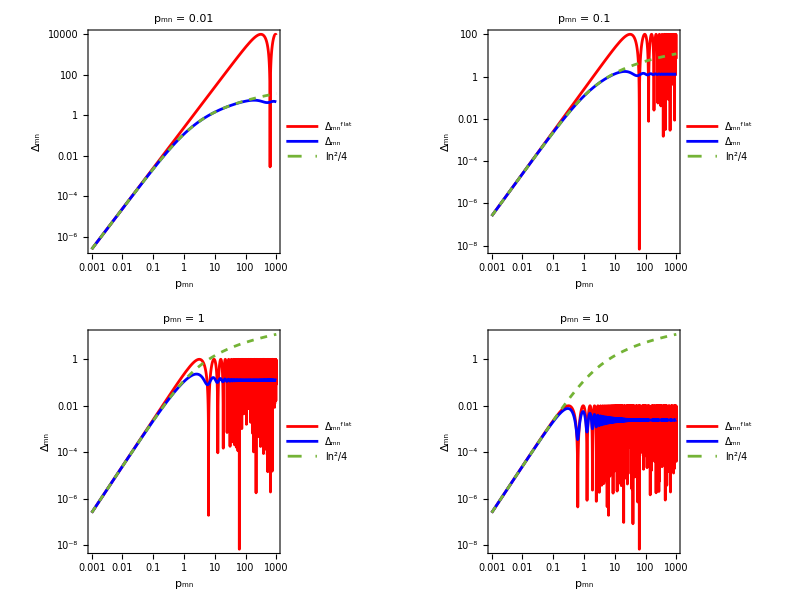

```mathematica
Pmns=10^Range[-2,1];
Table[Plot[{SSModel`Private`ΔmnFlatOverH2[δτH,Pmn],Δmn[δτH,Pmn],Log[δτH+1]^2/4},{δτH,10^-3,10^3},
ScalingFunctions->{"Log","Log"},
ImageSize->Medium,
PlotStyle->{Red,Blue,Dashed},
Frame->True,FrameLabel->{"p_mn","Δ_mn"},
PlotLegends->Placed[{"Δ_mn^flat","Δ_mn","ln^2/4"},{Left,Top}],
PlotLabel->StringTemplate["p_mn = ``"][Pmn]],
{Pmn,Pmns}]//Partition[#,2]&//Grid
```

#### Δ_mn

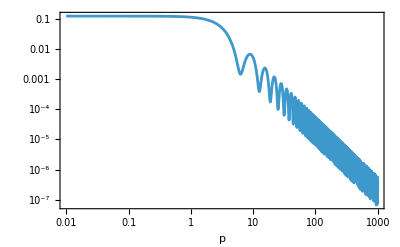

```mathematica
LogLogPlot[Δmn[δτH,Q]/.num,{Q,10^-2,10^3},$PlotOptions//Evaluate]
```

```mathematica
Flatten[Table[{m,n},{m,{-1,1}},{n,{-1,1}}],1]
```

{{-1,-1},{-1,1},{1,-1},{1,1}}

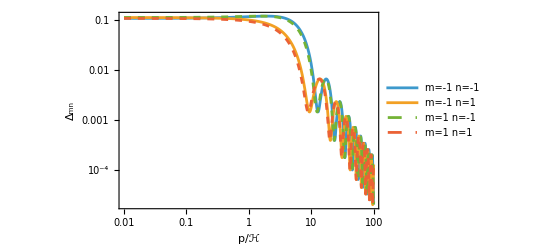

```mathematica
LogLogPlot[Table[Δmn[δτH,{m,n},{k,Q,𝓆,cs=1./√3}]/.num,{m,{-1,1}},{n,{-1,1}}]//Evaluate,{Q,10^-2,10^2},
FrameLabel->{"p/ℋ", "Δ_mn"},PlotStyle->{Dashing[None],Dashing[None],Dashed,Dashed},
PlotLegends->Flatten[Table[StringTemplate["m=`` n=``"][m,n],{m,{-1,1}},{n,{-1,1}}],1],
$PlotOptions//Evaluate]
```

## GW Spectrum

Ω_GW(δτ_fin,K) = 3 ((w̄)/((ρ̄)_d))^2 (((ρ̄)_d)/((ρ̄)_tot))^2 (E_kin^*/(R_*))^2 𝒯_GW (g_*) K^3  ∫_-1^1 ⅆz (1-z^2)^2∫_0^∞ dp p^2/((p̃)^4(k,p,z))ζ_kin(p)ζ_kin(p̃)Δ(δτ,K,p,p̃)
	=3 ((w̄)/((ρ̄)_d))^2 (((ρ̄)_d)/((ρ̄)_tot))^2 (E_kin^*/(R_*))^2 𝒯_GW (g_*) K^2  ∫_o^∞ ⅆp p ζ_kin(p)∫_0^∞ d p̃ 1/(p̃)^3 ζ_kin(p̃)Δ(δτ,K,p,p̃)

```mathematica
GWpaper=Import["/home/marco/PhD/DarkTransitions/data/digitized_plot_vw_.9.csv","Dataset"];
```

```mathematica
GWpaperᵀ[All,{"kR_star","Omega_GW_RH0p01"}]ᵀ
```

Transpose[Failure[Dataset,{MessageTemplate:>Dataset::partnotapplicable,MessageParameters→{Type→TypeSystem`Vector[TypeSystem`Atom[Real],300],Part→{kR_star,Omega_GW_RH0p01},Symbol→Part}}]]

```mathematica
Υ2f[.1]
```

Υ2f[0.1]

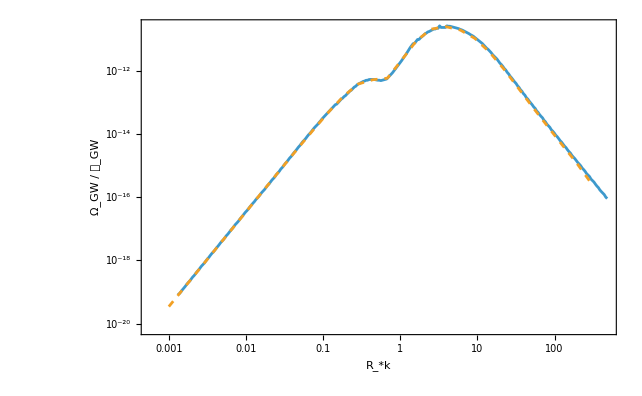

```mathematica
PlotGWData[Join[{{"kR_star",1/11^2/2.3 "Omega_GW_RH0p01"}/.Normal[GWpaper]},Normal[GWData[Select[#SourceDuration==.1∧#vw==.9∧#HR==.01&]][All,"KOmega"]]],PlotStyle->{Automatic,Dashed}]
```

### 1 Fluid

#### Ω_GW(K)

Option 1: get the kinetic spectrum from ξ_w and α

```mathematica
OmegaGW[.1,{cs,δτH,HR},{vw,α},"DensityFraction"->ρFrac]/.num//EchoTiming
```

Loaded kinetic spectrum with parameters:

0.458114

5.26748×10^-14

Option 2: pass the kinetic spectrum by hand

```mathematica
KSpectrum=GetKineticSpectrum[.5,.1,cs=1./√3]//Quiet;
AutoComplete[KSpectrum];
```

Loaded kinetic spectrum with parameters:

```mathematica
KSpectrum["KSpectrum"][1.]
```

0.129509

```mathematica
OmegaGW[1.,{cs,δτH,HR}/.num,KSpectrum,"DensityFraction"->ρFrac]//EchoTiming
```

2.24662

1.1113×10^-9

#### Compute spectrum

```mathematica
gw=ComputeOmegaGW[{cs,δτH,HR}/.num,{vw,α}/.num,
"DensityFraction"->ρFrac,
"Verbose"->True,
"N"->100,
"KRange"->{10.^-3,3 10.^2},
"Store"->"data/GWSpectra.1f.wl"
	];
```

Loaded kinetic spectrum with parameters:

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

2972.68

100/100 (100%) points computed

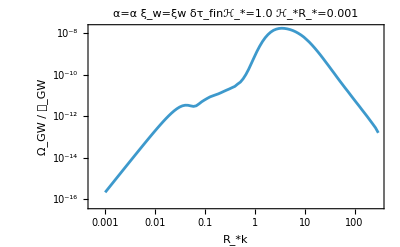

```mathematica
PlotGWData[gw]
```

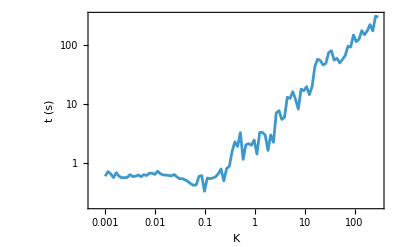

```mathematica
PlotTiming[gw]
```

```mathematica
$Verbose=False;
```

```mathematica
Get[file1f]
```

Parallel evaluation

```mathematica
ParallelEvaluate[SetDirectory[NotebookDirectory[]];
Import["SSModel/SSModel.wl"];//Quiet]
```

Loaded/home/marco/PhD/DarkTransitions/SSModel/BubbleFluidProfiles.wl

Loaded/home/marco/PhD/DarkTransitions/SSModel/BubbleFluidProfiles.wl

Loaded/home/marco/PhD/DarkTransitions/SSModel/BubbleFluidProfiles.wl

«7 more identical outputs»

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

Loaded/home/marco/PhD/DarkTransitions/SSModel/BubbleFluidProfiles.wl

Loaded/home/marco/PhD/DarkTransitions/SSModel/BubbleFluidProfiles.wl

Loaded/home/marco/PhD/DarkTransitions/SSModel/BubbleFluidProfiles.wl

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

Loaded/home/marco/PhD/DarkTransitions/SSModel/BubbleFluidProfiles.wl

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

«3 more identical outputs»

Auxiliary parameters set to:

Auxiliary parameters set to:

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

Auxiliary parameters set to:

Auxiliary parameters set to:

$DataFolder folder set to /home/marco/PhD/DarkTransitions/SSModel/data.
Redefine $DataFolder to set new data path.

Auxiliary parameters set to:

Auxiliary parameters set to:

Auxiliary parameters set to:

«3 more identical outputs»

c_s^2 →  1/3

c_s^2 →  1/3

Auxiliary parameters set to:

Auxiliary parameters set to:

Auxiliary parameters set to:

c_s^2 →  1/3

c_s^2 →  1/3

Auxiliary parameters set to:

c_s^2 →  1/3

c_s^2 →  1/3

c_s^2 →  1/3

«3 more identical outputs»

Γ_ad →  1.33333

Γ_ad →  1.33333

c_s^2 →  1/3

c_s^2 →  1/3

c_s^2 →  1/3

Γ_ad →  1.33333

Γ_ad →  1.33333

c_s^2 →  1/3

Γ_ad →  1.33333

Γ_ad →  1.33333

Γ_ad →  1.33333

«7 more identical outputs»

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
ParallelTable[
a=<|"vw"->vw,"SourceDuration"->δτH,"HR"->HR|>;
If[Length[FilterDataset[file1f,a]]>0,
Print["Skipping ",a],
Echo[a,"Computing"];
gw=ComputeOmegaGW[{cs,δτH,HR},{vw,α/.num},
"DensityFraction"->ρFrac,
"N"->30,
"Verbose"->False,
"DynamicPlot"->False,
"KRange"->{10.^-3,3 10.^2},
"Store"->file1f
];
Echo[StringRiffle[{vw,δτH,HR}],TimeObject[]]
],
{vw,1.Range[1,9,2]/10},
{δτH,{.01}},
{HR,{.01,.001}}
]
```

Computing  <|vw→0.1,SourceDuration→0.01,HR→0.01|>

Computing  <|vw→0.1,SourceDuration→0.01,HR→0.001|>

Computing  <|vw→0.3,SourceDuration→0.01,HR→0.01|>

Computing  <|vw→0.3,SourceDuration→0.01,HR→0.001|>

Computing  <|vw→0.5,SourceDuration→0.01,HR→0.01|>

Computing  <|vw→0.5,SourceDuration→0.01,HR→0.001|>

Computing  <|vw→0.7,SourceDuration→0.01,HR→0.01|>

Computing  <|vw→0.7,SourceDuration→0.01,HR→0.001|>

Computing  <|vw→0.9,SourceDuration→0.01,HR→0.01|>

Computing  <|vw→0.9,SourceDuration→0.01,HR→0.001|>

53.5009

20:45:43TimeObject[{20,45,43.272282},Instant]  0.5 0.01 0.01

55.7836

20:45:45TimeObject[{20,45,45.415168},Instant]  0.3 0.01 0.01

59.6526

20:45:49TimeObject[{20,45,49.38824},Instant]  0.7 0.01 0.01

67.4516

20:45:56TimeObject[{20,45,56.98782},Instant]  0.1 0.01 0.01

72.3801

20:46:01TimeObject[{20,46,1.960214},Instant]  0.9 0.01 0.01

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

222.699

20:48:32TimeObject[{20,48,32.28923},Instant]  0.5 0.01 0.001

223.81

20:48:33TimeObject[{20,48,33.283428},Instant]  0.9 0.01 0.001

228.899

20:48:38TimeObject[{20,48,38.385362},Instant]  0.3 0.01 0.001

237.053

20:48:46TimeObject[{20,48,46.466599},Instant]  0.1 0.01 0.001

275.408

20:49:24TimeObject[{20,49,24.935318},Instant]  0.7 0.01 0.001

{{{0.1 0.01 0.01,0.1 0.01 0.001}},{{0.3 0.01 0.01,0.3 0.01 0.001}},{{0.5 0.01 0.01,0.5 0.01 0.001}},{{0.7 0.01 0.01,0.7 0.01 0.001}},{{0.9 0.01 0.01,0.9 0.01 0.001}}}

#### Breakdown of the integration

```mathematica
ζk=KSpectrum["KSpectrum"];
```

```mathematica
ΔN[p_,𝓅_]:=Δ[δτH,{k/HR,p/HR,𝓅/HR,cs}]/.num//Simplify//Evaluate
```

```mathematica
OmegaGWIntegrand[ζk,ΔN,{k,0.,2.}/.num]//EchoTiming
```

0.002886

0.00696813+0. ⅈ

```mathematica
OmegaGWIntegrandP[ζk,ΔN,{k,0.}/.num]//EchoTiming
```

0.200063

0.000487856

#### Visualize data

```mathematica
data=Get[file1f]
```

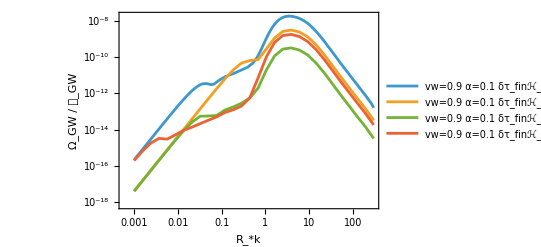

```mathematica
PlotGWData[data[Select[#vw==0.9&]]]
```

```mathematica
data[Select[#vw==.5∧#SourceDuration==1.∧#HR==.001&]]
```

```mathematica
data[Select[#vw==.5∧#SourceDuration==1.∧#HR==.001&]][All,"KTime"]//Normal//Dimensions
```

{1,30,2}

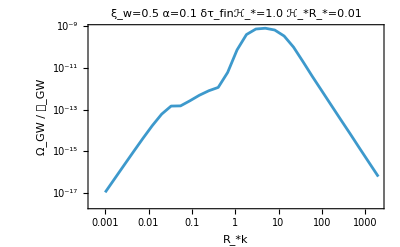

```mathematica
PlotGWData[data[1]//Normal]
```

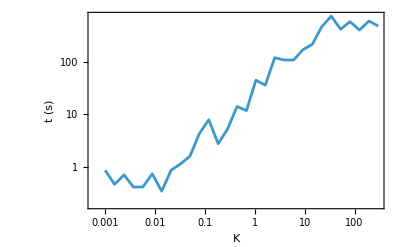

```mathematica
PlotTiming[data[Select[#vw==.5∧#SourceDuration==1.∧#HR==.001&]]]
```

### 2 Fluids

The spectrum implemented is the same as for 1 fluid, except for the “modified Δ time integral”
Ω_GW^(2f)(δτ_fin,K,{γ,r_w}) = 3 ((w̄)/((ρ̄)_d))^2 (((ρ̄)_d)/((ρ̄)_tot))^2 (E_kin^*/(R_*))^2 K^3 𝒯_GW (g_*)   ∫_-1^1 ⅆz (1-z^2)^2∫_0^∞ dp p^2/((p̃)^4(k,p,z))ζ_kin(p)ζ_kin(p̃)Δ^(2f)(δτ,K,p,p̃,{γ,r_w})

```mathematica
num[γ]=100.
```

100.

```mathematica
Ks=LogSubdivide[10^-3,3 10^2,30]
```

{0.001,0.00152255,0.00231815,0.00352949,0.00537382,0.00818189,0.0124573,0.0189668,0.0288779,0.043968,0.0669433,0.101924,0.155185,0.236276,0.359741,0.547723,0.833933,1.2697,1.93318,2.94336,4.4814,6.82315,10.3886,15.8171,24.0822,36.6664,55.8262,84.9981,129.414,197.038,300.}

```mathematica
Ks[[21]]
```

4.4814

```mathematica
gw=OmegaGW[1.,{cs,δτH,HR},{vw,α},"DensityFraction"->ρFrac]/.num//EchoTiming
```

Loaded kinetic spectrum with parameters:

1.86029

6.93108×10^-12

```mathematica
ComputeOmegaGW2f[{cs,δτH,HR}/.num,{vw,α}/.num,{γ,r}/.num,"KRange"->{10.^-3,2 10.^-3},"N"->2,"Store"->file2f,"Verbose"->False]
```

$Aborted

```mathematica
ParallelEvaluate[SetDirectory[NotebookDirectory[]];
Import["SSModel/SSModel_2f.wl"];//Quiet]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
ParallelTable[
a=<|"vw"->vw,"SourceDuration"->δτH,"HR"->HR,"γ"->γ|>;
If[Length[FilterDataset[file2f,a]]>0,
Print["Skipping ",a],
Echo[a,"Computing"];
gw=ComputeOmegaGW2f[{cs,δτH,HR},{vw,α/.num},{γ,r/.num},
"DensityFraction"->ρFrac,
"N"->30,
"Verbose"->False,
"DynamicPlot"->False,
"KRange"->{10.^-3,3 10.^2},
"Store"->file2f,
MaxRecursion->1
];
Echo[StringRiffle[{vw,δτH,HR,γ}],TimeObject[]]
],
{vw,1.Range[1,9,2]/10},
{δτH,{.01}},
{HR,{.01,.001}},
{γ,If[HR===.01,{10.},{10.,100.}]}
]
```

Skipping <|vw→0.1,SourceDuration→0.01,HR→0.01,γ→10.|>

Skipping <|vw→0.1,SourceDuration→0.01,HR→0.001,γ→10.|>

Skipping <|vw→0.1,SourceDuration→0.01,HR→0.001,γ→100.|>

Skipping <|vw→0.3,SourceDuration→0.01,HR→0.01,γ→10.|>

Skipping <|vw→0.3,SourceDuration→0.01,HR→0.001,γ→10.|>

Skipping <|vw→0.3,SourceDuration→0.01,HR→0.001,γ→100.|>

Skipping <|vw→0.5,SourceDuration→0.01,HR→0.01,γ→10.|>

Skipping <|vw→0.5,SourceDuration→0.01,HR→0.001,γ→10.|>

Computing  <|vw→0.5,SourceDuration→0.01,HR→0.001,γ→100.|>

Skipping <|vw→0.7,SourceDuration→0.01,HR→0.01,γ→10.|>

Skipping <|vw→0.7,SourceDuration→0.01,HR→0.001,γ→10.|>

Skipping <|vw→0.7,SourceDuration→0.01,HR→0.001,γ→100.|>

Skipping <|vw→0.9,SourceDuration→0.01,HR→0.01,γ→10.|>

Skipping <|vw→0.9,SourceDuration→0.01,HR→0.001,γ→10.|>

OptionValue::nodef: Unknown option MaxRecursion for {ComputeOmegaGW,OmegaGWPref,GetKineticSpectrum}.

Skipping <|vw→0.9,SourceDuration→0.01,HR→0.001,γ→100.|>

OptionValue::nodef: Unknown option Store for GetKineticSpectrum.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 1 recursive bisections in SSModel2f`Private`logP near {SSModel2f`Private`logP} = {1.01604}. NIntegrate obtained 2.29216×10^-10 and 1.62444×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 1 recursive bisections in SSModel2f`Private`logP near {SSModel2f`Private`logP} = {0.00399455}. NIntegrate obtained 1.48997×10^-10 and 2.06507×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 1 recursive bisections in SSModel2f`Private`logP near {SSModel2f`Private`logP} = {1.01604}. NIntegrate obtained 8.80034×10^-10 and 4.53499×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

26.5837

00:35:25TimeObject[{0,35,25.347794},Instant]  0.5 0.01 0.001 100.0

{{{{Null},{Null,Null}}},{{{Null},{Null,Null}}},{{{Null},{Null,0.5 0.01 0.001 100.0}}},{{{Null},{Null,Null}}},{{{Null},{Null,Null}}}}

```mathematica
gw=FilterDataset[data,<|"SourceDuration"->1.,"vw"->.5,"HR"->.01|>]
```

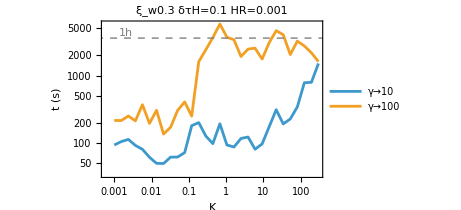

```mathematica
PlotTiming[gw,Epilog->{Gray,Dashed,InfiniteLine[Log@{1,3600},{1,0}],Text["1h",Log@{2 10^-3,1.2 3600}]},PlotLabel->StringTemplate["ξ_w`vw`   δτH=`SourceDuration`   HR=`HR`"][gw[1]//Normal],
ImageSize->Medium,
PlotLegends->{"γ→10","γ→100"}]
```

## Paper plots

### Fig. 1

```mathematica
leg=;
```

```mathematica
plots=PlotGWSuppressions[.9,"Data1f"->"cosmo","Data2f"->"cosmo","r"->1.,PlotRange->10^{-18,-8}];
```

```mathematica
grid=PlotGrid[plots]
```

```mathematica
fig=Overlay[{Overlay[{PlotGrid[grid,Spacings->5],leg[[All,;;2]]},Alignment->{-.8,.85}],leg},Alignment->{.3,.85}]
```

-Graphics-

```mathematica
Export["figs/vw_.9_.png",fig,ImageResolution->200]
```

### Fig. 2

```mathematica
dτs=10.^Range[-1.,0];
Table[PlotPrefactor[δτH]//Quiet
,{δτH,dτs}]//PlotGrid[{#},ImageSize->650,Spacings->5]&
```

General::munfl: Exp[-813.369] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
Export["/home/marco/PhD/DarkTransitions/figs/Prefactor/pref_ratio_dtau_paper.pdf",%183,ImageResolution->200]
```

General::munfl: Exp[-813.369] is too small to represent as a normalized machine number; precision may be lost.

/home/marco/PhD/DarkTransitions/figs/Prefactor/pref_ratio_dtau_paper.pdf